```mathematica
ClearAll["Global`*"]
```

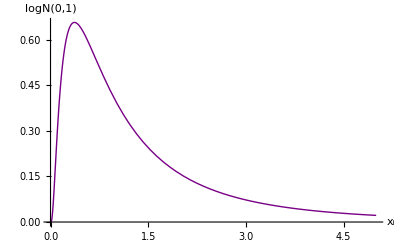

```mathematica
Plot[PDF[LogNormalDistribution[0,1],x],{x,0,5},ColorFunction->Function[{x,y},If[x>0.3678794495424417,Red,Blue]],ColorFunctionScaling->False,
PlotStyle->Thick,AxesLabel->{"x_i","logN(0,1)"}, PlotRange->Automatic]
```

```mathematica
FindMaximum[PDF[LogNormalDistribution[0,1],x],x]
```

{0.657745,{x→0.367879}}

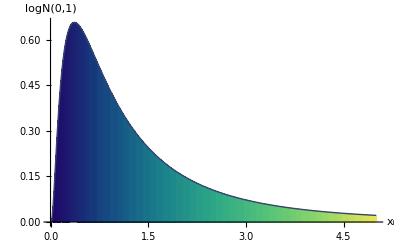

```mathematica
Plot[PDF[LogNormalDistribution[0,1],x],{x,0,5},ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x]],
PlotStyle->Thick,AxesLabel->{"x_i","logN(0,1)"}, PlotRange->Automatic, Filling->Axis]
```